## 5.9.a

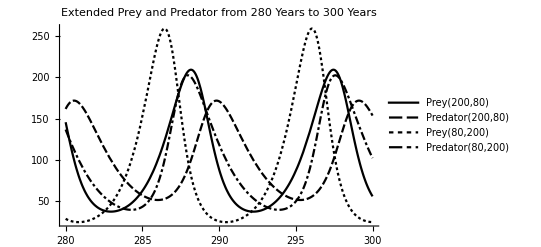

```mathematica
Module[{β1,c1,p1,c2,α2,p2,diff,soln,x0,y0},
β1=1;
α2=0.5;
c1=0.01;
c2=0.005;
p1=0;
p2=0;
diff[x0_,y0_]=
{X'[t]==β1 X[t]-c1 X[t] Y[t]-p1 X[t],
X[0]==x0,
Y'[t]==c2 X[t] Y[t]-α2 Y[t]-p2 Y[t],
Y[0]==y0};
soln[x0_,y0_]:=NDSolve[diff[x0,y0],{X,Y},{t,0,300}];
Plot[Evaluate[{X[t]/.soln[200,80],Y[t]/.soln[200,80],
X[t]/.soln[80,200],Y[t]/.soln[80,200]}],
{t,280,300},
PlotRange->{All,{0,All}},
PlotTheme->"Monochrome",
PlotLabel->"Extended Prey and Predator from 280 Years to 300 Years",
PlotLegends->{"Prey(200,80)","Predator(200,80)","Prey(80,200)","Predator(80,200)"}]
]
```

## 5.9.b

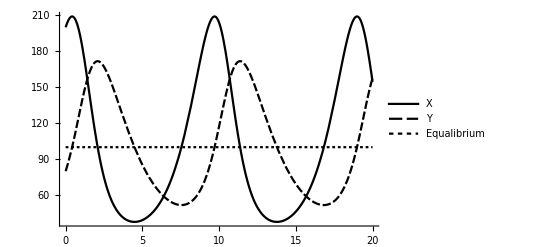

```mathematica
Module[{β1,c1,p1,c2,α2,p2,diff,soln,x0,y0},
β1=1;
α2=0.5;
c1=0.01;
c2=0.005;
p1=0;
p2=0;
diff[x0_,y0_]=
{X'[t]==β1 X[t]-c1 X[t] Y[t]-p1 X[t],
X[0]==x0,
Y'[t]==c2 X[t] Y[t]-α2 Y[t]-p2 Y[t],
Y[0]==y0};
soln[x0_,y0_]:=NDSolve[diff[x0,y0],{X,Y},{t,0,20}];
Plot[Evaluate[{X[t],Y[t],100}/.soln[200,80]],
{t,0,20},
PlotRange->{All,{0,All}},
PlotTheme->"Monochrome",
PlotLegends->{"X","Y","Equalibrium"}]
]
```

## 5.9.c

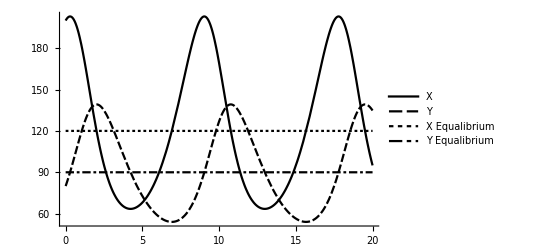

```mathematica
Module[{β1,c1,p1,c2,α2,p2,diff,soln,x0,y0},
β1=1;
α2=0.5;
c1=0.01;
c2=0.005;
p1=.1;
p2=.1;
diff[x0_,y0_]=
{X'[t]==β1 X[t]-c1 X[t] Y[t]-p1 X[t],
X[0]==x0,
Y'[t]==c2 X[t] Y[t]-α2 Y[t]-p2 Y[t],
Y[0]==y0};
soln[x0_,y0_]:=NDSolve[diff[x0,y0],{X,Y},{t,0,20}];
Plot[Evaluate[{X[t],Y[t],120,90}/.soln[200,80]],
{t,0,20},
PlotRange->{All,{0,All}}, 
PlotTheme->"Monochrome",
PlotLegends->{"X","Y","X Equalibrium","Y Equalibrium"}]
]
```